# Как использовать компиляцию

## В этой лекции будет рассмотрен синтаксис функции Compile[], типизация аргументов, основные опции, ограничения Compile[].

### Зачем нужна компиляция в Mathematica?

Значительно повышает скорость вычислений

По типу исполнения - Mathematica является интерпретируемым языком с динамической типизацией. Как и любые другие языки подобного типа, Wolfram Language значительно уступает в быстродействии компилируемым языкам

Больший контроль кода, меньшая вероятность ошибок

По причине динамической типизации в “шаблонных” и чистых функциях осуществлять контроль преобразований достаточно тяжело. Скомпилированный код при этом проходит более строгую проверку

Позволяет создавать автономные исполняемые файлы и динамические библиотеки

Создание такого рода приложений в большей степени требует знания языка C вместе с Wolfram Language, поэтому в данной лекции эта функциональность не будет рассмотрена

### Основной синтаксис Compile[]

Синтаксис Compile[] и Function[] очень похож. 
Функция принимает в качестве входных параметров два аргумента:

Compile[{variable, ...}, expression]

Первый - список аргументов результирующей функции

Второй - выражение, которое будет скомпилировано

Результат, который возвращает функция Compile[] - это другая функция, ее применение выполняет выражение expression над переданными функции аргументами - variable

Постой пример скомпилированной функции, сравнение с чистой и обычной функцией:

Здесь и далее для разделения похожих функций будем использовать такое обозначение:

rFunctionName - от слова regular - обычная функция

nFunctionName - от слова normal - чистая функция

cFunctionName - от слова compile - скомпилированная функция

```mathematica
(* 
	Создадим три функции для проверки: 
	rFuncQuadAdd; nFuncQuadAdd; cFuncQuadAdd
*)
rFuncQuadAdd[x_] := x + x^2 + x^3 + x^4 + x^5
nFuncQuadAdd = Function[x, x + x^2 + x^3 + x^4 + x^5]
cFuncQuadAdd = Compile[x, x + x^2 + x^3 + x^4 + x^5]
```

Function[x,x+x^2+x^3+x^4+x^5]

CompiledFunction[…]

```mathematica
AbsoluteTiming[rFuncQuadAdd[10.0]]
AbsoluteTiming[nFuncQuadAdd[10.0]]
AbsoluteTiming[cFuncQuadAdd[10.0]]
```

{0.0000162,111110.}

{8.2×10^-6,111110.}

{0.0004301,111110.}

```mathematica
cf = Compile[{x, y, z}, x + y + z]
```

CompiledFunction[…]

```mathematica
cf[1, 2, 3]
```

6.

Тест работы созданных функций:

```mathematica
(* Тест на различных аргументах - Pi/I/0/1/... *)
```

Тест быстродействия созданных функций:

```mathematica
(* для теста создадим список из 2000 случайных чиcел - testNumList *)
```

```mathematica
(* теперь простым циклом пройдемся по всему списку складывая числа *)
```

### Явное указание типов аргументов в Compile[]

Указать то, что итоговая функция будет работать с аргументами определенных типов можно непосредственно при создании скомпилированной функции. Общая конструкция должная выглядеть так:

Compile[{{variable, _Type}}, expression]

Здесь _Type - явный тип аргумента функции. В скомпилированную функцию можно передавать аргументы следующих типов:

True|False - логические значения

```mathematica
(* две "одинаковые" функции (cBoolToIntI; cBoolToIntR), каждая переводит булево значение в 0 и 1 соответственно *)
```

```mathematica
(* кто попытется объяснить различия получаемых результатов *)
```

_Integer - целое число

```mathematica
(* Функция (cIntPlusHalf), которая увеличивает целое число в 1.5 раз и округляет *)
```

```mathematica
(* кто попытается объяснить полученный результат для: 2; 2.; 21/10; 2.1; 2.0 + 10.^-19 *)
```

_Real - действительное число с плавающей точкой, а так же это тип по умолчанию

```mathematica
(* функция, возвращающая длину трехмерного вектора - cNorma*)
```

```mathematica
(* Кто объяснит полученные результаты? {-0, 1, 2.}; {1, E, Pi} *)
```

_Complex - комплексное число

```mathematica
(* функция, которая увеличивает реальную часть комплексного числа - cIncrRe *)
```

```mathematica
(* попробуйте объяснить результат 3 + I; 3.; 3. + Exp[I 7] *)
```

Пример скомпилированной функции с явным указанием типов аргументов:

```mathematica
f1 = Compile[{{n, _Integer}, {x, _Real}, {z, _Complex}}, n + x + z]
```

CompiledFunction[…]

```mathematica
f1[1, 1, 1]
f1[1 + I, 1, 1]
```

3.+0. ⅈ

CompiledFunction::cfsa: Argument 1+ⅈ at position 1 should be a machine-size integer.

3+ⅈ

```mathematica
1 + I + 1 + 1
```

3+ⅈ

```mathematica
f[x_] := x + 1
f["string"]
f[1]
```

1+string

2

```mathematica
(* Гамма функция Эйлера *)
cGammaEuler = 
Compile[{{m, _Integer}, {z, _Complex}}, 
	(1/z) * Apply[Times, Table[((1 + 1/n)^z)/(1 + z/n), {n, 1, m}]]]
```

CompiledFunction[…]

```mathematica
AbsoluteTiming[cGammaEuler[10, 1.0]]
AbsoluteTiming[((1/1.0) * Apply[Times, Table[((1 + 1/n)^1.0)/(1 + 1.0/n), {n, 1, 10}]])]
```

{0.0000204,1.+0. ⅈ}

{0.0000424,1.}

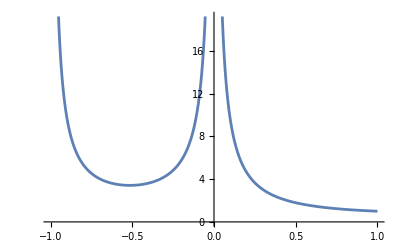

```mathematica
Plot[Abs[cGammaEuler[10, z]], {z, -1, 1}]
```

### Передача тензоров в качества аргументов Compile[]

```mathematica
{1, 1, 1, 1, 1}
{1, 1, 1, 1, {1}}
{{{1, 2}, {3, 4}}, {{5, 6}, {7.0 + I, 8}}}
```

Одним из самых полезных свойств Compile[] является возможность работы с тензорами. Создать функцию, в которую в качестве аргумента можно передать тензор так же просто как и в двух предыдущих случаях. Требуется добавить только размерность аргумента:

Compile[{{variable, _Type, dimension}}, expression]

Здесь dimension - размерность передаваемого тензора. Если ничего не указывать - то во всех предыдущих случаях это значение было 0, 1 - одномерный тензор, 2 - двумерный и так далее

Почему именно Тензор? Ведь можно сказать Массив (как в Delphi) или список (как в Mathematica). Тем более, что по факту, применять скомпилированную функцию надо именно к списку. Определение Тензор выделяет из всевозможных списков, поддерживаемых Математикой только те, которые являются однородными относительно размерности - то есть размерность вложенных списков на каждом уровне одинакова. А так же все элементы каждого конечного списка принадлежат одному типу. Тип должен быть один из поддерживаемых функцией Compile[].

Пример создания функции, принимающей в качестве аргумента Тензор

```mathematica
(* Функция которая возвращает для одномерного списка модуль или аргумент в зависимости от отношения реальной и мнимой часи *)
cAbsOrArg = Compile[{{points, _Complex, 1}}, 
	Table[If[Re[point] > Im[point], Arg[point], Abs[point]], {point, points}]]
```

CompiledFunction[…]

Если скомпилированная функция на вход принимает только тензор, то что она может возвращать?

Все ограничение на возвращаемый результат такие же как и ограничения на входные параметры. Если скомпилированные функции на вход принимают только тензоры, то возвращать могут тоже только тензоры. Все элементы тензора обязаны быть однотипны. Покажем несколько правильных и неправильных примеров.

```mathematica
(* 
	работающий код - функция сReImAbsArg, 
	которая вернет модуль, аргумент, действительную 
	и реальную часть комлексного числа списком 
*)
cAbsOrArgErr = Compile[{{points, _Complex, 1}}, 
	Table[{Re[point], Im[point], Arg[point], Abs[point], {point}}, {point, points}]]
```

CompiledFunction[…]

```mathematica
(* проверим как она работает на Pi+I*E *)
cAbsOrArgErr[{1 + I}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 17; proceeding with uncompiled evaluation.

{{1,1,π/4,√2,{1+ⅈ}}}

```mathematica
(* теперь тоже самое, но попробуем вернуть список такого вида сReImAbsArgErr[z] -> {z, {re, im, abs, arg}} *)
```

```mathematica
(* попробуйте объяснить полученный результат *)
```

### Использование локальных переменных внутри Compile[]

Способы локализации переменных внутри Compile[]. Синтаксис точно такой же как и для любой другой функции. Самое главное в этом - понимать что использовать локализующие функции можно благодаря тому, что компиляция их поддерживает.

Compile[{{variable, _Type, dimension}}, Module[{localvriable}, expression]]
Compile[{{variable, _Type, dimension}}, Block[{localvriable}, expression]]
Compile[{{variable, _Type, dimension}}, With[{localvriable = anothervariable}, expression]]

Краткое напоминание по функциям:

Module[{m}, expr] - создает локальную переменную m внутри Module[], которая в итоге не видна в окружающем контексте

Block[{b}, expr] - очищает определения для b и после завершения выполнения возвращает в первоначальное состояние

With[{w = g}, expr] - для локальной переменной w используется внешнее определение. Позволяет создать копию, которую можно изменять не опасаясь поломки кода.

Пример создания функции, внутри определения которой используются локальные переменные:

```mathematica
(* Рассчет силы тяжести. Простой пример - используется пять локальных переменных и переобозначения для удобства - все внутри Module *)
cGForce = Compile[{{pointa, _Real, 1}, {pointA, _Real, 1}}, 
	Module[
		{
			G = 6.67384 * 10^-11,
			R, Fx, Fy, Fz,
			m = pointa[[1]],
			x = pointa[[2]],
			y = pointa[[3]],
			z = pointa[[4]],
			M = pointA[[1]],
			X = pointA[[2]],
			Y = pointA[[3]],
			Z = pointA[[4]]
		}, 

		R = ((X - x)^2 + (Y - y)^2 + (Z - z)^2)^(1/2);
		Fx = ((X - x)/R) * G M m / R^2;
		Fy = ((Y - y)/R) * G M m / R^2;
		Fz = ((Z - z)/R) * G M m / R^2;
		{Fx, Fy, Fz}
	]
]
```

CompiledFunction[…]

```mathematica
cGForce[{400000000., 1.0, 1.0, 7.3 * 10^22}, {0, 0, 0, 5.97*10^24}]
```

{0.,0.,0.}

WolframAlphaQueryParseResults

5.97×10^24 kg

### Опции Compile[]

Как у любой другой функции у Compile[] существует некоторый набор опций. Перечислим их:

Compile[{var}, expr, CompilationTarget -> ...]
Compile[{var}, expr, Parallelization -> ...]
Compile[{var}, expr, CompilationOptions -> ...]
Compile[{var}, expr, RuntimeAttributes -> ...]
Compile[{var}, expr, RuntimeOptions -> ...]

Пояснение каждой опции

CompilationTarget - указание цели компиляции. Имеется ввиду итоговый результат компиляции - машинный код скомпилированный из C кода и байт-код, полученный из кода для виртуальной машины Математики. Соответственно значений у данной опции может быть два: 
	CompilationTarget → “C”
	CompilationTarget → “MVM” (значение по умолчанию)

RuntimeAttributes & Parallelization - указание для использования итоговой функции в многопоточном режиме. Позволяет ускорить выполнение функций, которые применяются к списку. Кроме того просто указание атрибута Listable позволяет применять функцию к списку значений:
	RuntimeAttributes → {Listable}
	Parallelization → False (значение по умолчанию)
	Parallelization → True

```mathematica
(* пример, показывающий различия во времени вычисления различных функций *)
```

CompilationOptions - тут все понятно интуитивно. Опция, которая указывает опции компиляции. =)
А на самом деле имеется три опции, которые не попали под категории, которые получили собственные имена как опции. Возможные значения:

CompilationOptions → {“ExpressionOptimization” → True} (по умолчанию Automatic) - указание компилятору делать (или не делать) оптимизацию выражения. Оптимизация заключается в повторном вычислении повторяющихся выражений

```mathematica
(* "ExpressionOptomization" -> False*)
cOptimazeFalse = Compile[{x}, x^2 + Sin[x^2]+Cos[x^2]+Exp[x^2] + Tan[x^2], CompilationOptions->{"ExpressionOptimization" -> False}]; 
(* "ExpressionOptomization" -> True*)
cOptimazeTrue = Compile[{x},  x^2 + Sin[x^2]+Cos[x^2]+Exp[x^2] + Tan[x^2], CompilationOptions->{"ExpressionOptimization" -> True}]; 

(* тест - кто попробует объяснить результат *)
RepeatedTiming[Do[cOptimazeFalse[1.4], {100000}]]
RepeatedTiming[Do[cOptimazeTrue[1.4], {100000}]]
```

CompilationOptions → {"InlineCompiledFunctions" → True} (по умолчанию False) - указание компилятору на возможность использования внешних скомпилированных функций
CompilationOptions → {"InlineExternalDefenition" → True} (по умолчанию False) - указание компилятору на использование внешних пользовательских функций
Все указанные опции выше очень интересны и полезны. Особенно использование внешних функций. Очень часто оказывается так, что куда проще написать несколько шаблонных функций, а затем использовать их в скомпилированной, чем писать целиком код шаблонных функций целиком. Примеры использования этих опций:

```mathematica
(* сначала создадим тестовую внешнюю функцию *)
cTestExternFunc[x_] := x^2 + 1

(* "InlineExternalDefinitions" -> False*)
cExternalCall = Compile[{x}, cTestExternFunc[x + 1] + 1, CompilationOptions->{"InlineExternalDefinitions" -> False}]; 

(* "InlineExternalDefinitions" -> True*)
cExternalDef = Block[{x, externalFuncRes}, 
	externalFuncRes = cTestExternFunc[x]; 
	Compile[{x}, externalFuncRes, CompilationOptions->{"InlineExternalDefinitions" -> True}]]; 

(* тест - кто попробует объяснить результат *)
RepeatedTiming[Do[cExternalCall[1.4], {1000}]]
RepeatedTiming[Do[cExternalDef[1.4], {1000}]]
```

RuntimeOptions → “Speed" - указание компилятору для ускорения кода
RuntimeOptions → “Quality” - указание компилятору для повышения точности
RuntimeOptions → {“EvaluateSymbolically” → False} - одна из самых полезных опций - возможность применения к символам
RuntimeOptions → ...

```mathematica
cf1 = Compile[x, x + 1, CompilationTarget->"MVM"]
```

CompiledFunction[…]

```mathematica
cf2 = Compile[x, x + 1, CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
RepeatedTiming[cf1[1]]
RepeatedTiming[cf2[1]]
```

```mathematica
3.4607372283935547*^-7/3.2729759216308595*^-7
```

1.05737

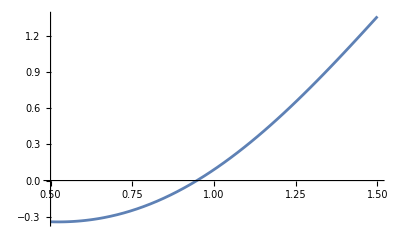

CompiledFunction::cfsa: Argument x at position 1 should be a machine-size real number.

{0.0625,{x→0.947743}}

{0.,{x→0.947743}}

```mathematica
(* функция, которая не может участвовать в решении уравнения *)
cFuncNonForEq = Compile[{{x, _Real}}, Sin[Total[Table[x + i, {i, -x, x, x/50000}]]/50000]]; 

(* функция, которая может участвовать в решении уравнения *)
cFuncForEq = Compile[{{x, _Real}}, Sin[Total[Table[x + i, {i, -x, x, x/50000}]]/50000], RuntimeOptions->{"EvaluateSymbolically"->False}]; 

(* график и нахоэжение численного решения*)
Plot[x - cFuncNonForEq[x], {x, 1/2, 3/2}]
Timing[FindRoot[x - cFuncNonForEq[x], {x, 1/2, 3/2}]]
Timing[FindRoot[x - cFuncForEq[x], {x, 1/2, 3/2}]]
```

```mathematica
cf = Compile[x, x+1, RuntimeOptions->{"EvaluateSymbolically"->False}]
```

CompiledFunction[…]

```mathematica
Solve[cf[x] == 0, x]
```

CompiledFunction::cfsa: Argument x at position 1 should be a machine-size real number.

{{x→-1}}

```mathematica
cf[a]
```

CompiledFunction::cfsa: Argument a at position 1 should be a machine-size real number.

1+a